# Datorövning 2: Visualisering

IX1307 Problemlösning i Matematik, Datorövning 1, HT2017

Notebook mall av Göran Andersson

## 1. Inledning

Data sammanställs ofta i tabeller, men det kan vara väldigt svårt att tyda data i den formen. Genom att visualisera data i ett diagram, blir det mycket tydligare vad datat representerar. Det blir enklare att jämföra resultat och man kan direkt se samband i diagrammet. Exempelvis om man ritar datapunkter i en graf kan det vara enkelt att se om det finns linjära- eller exponentiella funktioner som kan användas för att modellera datat.

## 2. Lärandemål

Efter datorövningen ska studenten kunna :

- använda datorbaserat matematikverktyg för visualisering.
- läsa matematisk text och sätta sig in i nya, matematiskt beskrivna, tillämpningsområden.

## 3. Diagram

### Hantering av data

Datapunkter hanteras som en lista av datapunkter {x, y}.

```mathematica
uidata={{1.0, 0.8}, {2.5, 1.6}, {4.0, 2.1}, {5.0, 2.7}, {6.5, 3.6}, {8.0, 4.2}}
```

{{1.,0.8},{2.5,1.6},{4.,2.1},{5.,2.7},{6.5,3.6},{8.,4.2}}

För att studera ett element kan man använda Part[] eller operatorn [[]]. För att få tredje datapunkten skriver man:

```mathematica
uidata[[3]]
```

{4.,2.1}

För att få x-värdet för tredje datapunkten skriver man

```mathematica
uidata[[3, 1]]
```

4.

och y-värdet:

```mathematica
uidata[[3, 2]]
```

2.1

Använd Mathematicas hjälp för att ta reda på mer information i “guide/ListManipulation”.

### Visualisering av data

Koldioxidhalten i atmosfären har ökat under hela 1900-talet. Följande data beskriver hur koldioxidhalten har ändrats mellan 1930 och 2015.

```mathematica
co2data={{1930, 297}, {1940, 306}, {1950, 314}, {1960, 319}, {1970, 326}, {1980, 339}, {1990, 354}, {2000, 369}, {2010, 389}, {2015, 400}};
```

Uppmätt data som representerar en tidsserie eller funktion kan bäst visualiseras med ett punktdiagram. Punktdiagram skapas med kommandot ListPlot.

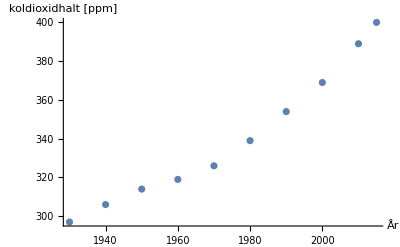

```mathematica
p1=ListPlot[co2data, AxesLabel->{"År", "koldioxidhalt [ppm]"}]
```

Använd Mathematicas hjälp-funktion för att ta reda på hur man kan rita grafen med ett rutnät och där punkterna är sammanbundna med linjer.

### Kurvanpassning

Med hjälp av funktionen FindFit kan man anpassa en modell till datapunkter. Här ett försök att anpassa en linjär modell till CO_2 datat i förgående exempel.

```mathematica
FindFit::usage
```

FindFit[data,expr,pars,vars] finds numerical values of the parameters pars that make expr give a best fit to data as a function of vars. 
FindFit[data,{expr,cons},pars,vars] finds a best fit subject to the parameter constraints cons.

```mathematica
{a1, b1}={a, b}/.FindFit[co2data, {a (t-1930)+b}, {a, b}, t]
```

{1.17756,288.898}

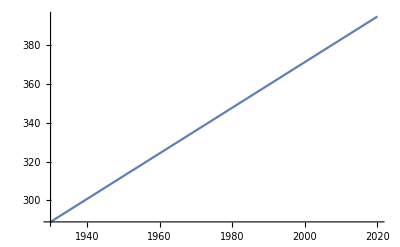

```mathematica
p2=Plot[a1 (t-1930)+b1, {t, 1930, 2020}]
```

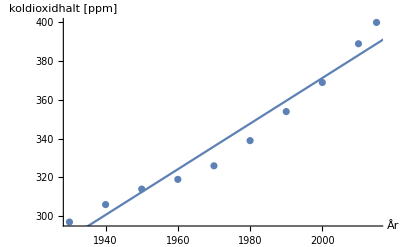

```mathematica
Show[p1, p2]
```

### Grafritning

Funktionen Plot används för att rita grafer av funktioner. Om man ska rita grafer för funktioner av två variabler kan man använda Plot3D. Plot finns också i varianter med Logaritmiska axlar: LogPlot, LogLogPlot och LogLinearPlot.

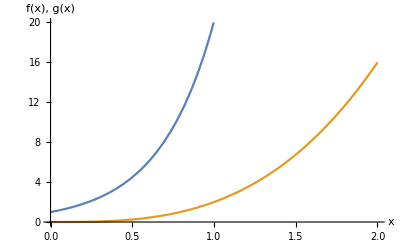

```mathematica
p1=Plot[{Exp[3x], 2x^3}, {x, 0, 2}, PlotRange->{{0, 2}, {0,20}}, AxesLabel->{"x", "f(x), g(x)"}]
```

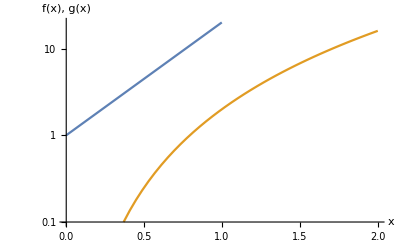

```mathematica
p2=LogPlot[{Exp[3x], 2x^3}, {x, 0, 2}, PlotRange->{{0, 2}, {0.1,20}}, AxesLabel->{"x", "f(x), g(x)"}]
```

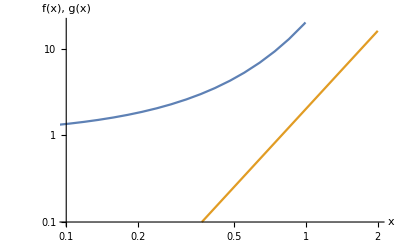

```mathematica
p3=LogLogPlot[{Exp[3x], 2x^3}, {x, 0, 2}, PlotRange->{{0.1, 2}, {0.1,20}}, AxesLabel->{"x", "f(x), g(x)"}]
```

```mathematica
p4=Plot3D[Cos[2x]Sin[3y], {x, 0, Pi}, {y,0, Pi}, AxesLabel->{"x", "y", "z"}]
```

-Graphics3D-

### Diagram och visualisering av information

Stapeldiagram används när data är kategoriserad i olika diskreta grupper. Höjden på stapeldiagrammet anger värdet för just den diskreta gruppen. Det finns inget funktionsvärde på x-axeln, bara en beteckning på den diskreta gruppen. Livslön för olika yrkesgrupper är följande

```mathematica
ll={19.1, 15.8, 15.9, 16.4, 18.3};
llLabel={"högskoleingenjör", "gymnasielärare","sjuksköterska", "gymnasieutbildning", "fysiker"};
```

```mathematica
ChartLabels->Placed[{"aaa","bbb","ccc"},Center,Rotate[#,45Degree]&]
```

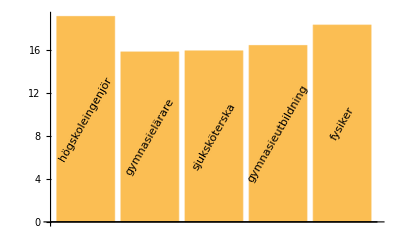

```mathematica
BarChart[ll,ChartLabels->Placed[llLabel, Center, Rotate[#, 60 Degree] &]]
```

Histogram används när data grupperas inom vissa intervall. Antal datapunkter som hamnar inom ett intervall anger y-värdet för just det intervallet. En tärning kan simuleras med hjälp av:

```mathematica
tSlag:= RandomInteger[{1, 6}];
```

1000 tärningslag med två tärningar

```mathematica
data=Table[tSlag+tSlag, {i, 1, 1000}];
```

Fördelningen kan visas i ett histogram :

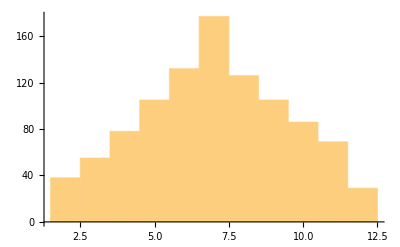

```mathematica
Histogram[data, 11]
```

Fördelningen mellan olika grupper kan anges i ett pajdiagram. Exempelvis är fördelning av fordon i Sverige (tusental fordon)

```mathematica
530+81
```

611

```mathematica
fdata={4760, 611, 14, 300, 76};
fnamn ={personbil, lastbil, buss, motorcykel, moped};
```

```mathematica
PieChart[fdata, ChartLegends->fnamn, ChartStyle->"DarkRainbow"]
```

-Graphics-

## 4. Övningsexempel

### Examensarbete

En student har genomfört ett examensarbete om trafikgenomströmningen på en landsväg, där hen har tagit fram relevant data för examensarbetet. Datat består av tre olika mätmängder: antalet fordon av olika fordonstyper som passerar genom landsvägen under en dag, samtliga motorfordons hastighet under 5 min (för kl 8, 12 och 17), fart på motorfordon och avstånd till motorfordonet framför under samma tidpunkt. Visualisera detta dataset på lämpliga sätt.

Antal fordon: cykel/moped, motorcykel, personbil, lätt lastbil, buss, tung lastbil.

```mathematica
aford={58, 6, 23, 3666,411,11, 63};
```

Hastighet för motorfordon som passerar mätpunkten under 5 min för kl 8, 12 och 17.

```mathematica
v08={68,71,70,78,92,62,79,71,79,73,87,86,85,85,73,92,100,64,78,85,86,82,72,81,78,73,71,76,92,93,81,94,78,77,82,70,79,63,76,83,82,64,76,71,79,78,71,88,79,72,88,65,81,78,65,71,86,91,81,82,69,90,92,98,79,83,71,52,88,74,68,75,83,91,70,91,84,78,92,83,61,96,75,70,80,91,69,78,79,85,74};
v12={75,64,53,84,94,83,86,70,73,84,88,80,81,65,81,103,59,82,79,67,81,81,72,72,89,96,83,83,68,87,72,56,78,64,82,81,94,81,87,74,83};
v17={97,76,84,57,75,77,78,91,65,78,72,92,73,87,77,67,82,65,75,70,73,85,85,81,83,79,65,80,73,76,69,101,63,71,70,91,95,80,86,77,81,85,75,92,92,77,91,82,83,78,72,77,91,89,62,57,91,73,77,81,66,70,73,75,71,82,87,65,75,73,77,87,83,89,84,69,90,84,80,80,75,102,79,69,71,88,63,65};
```

Hastighet och avstånd till framförvarande motorfordon under 5 min för kl 8, 12 och 17 (samma fordon som ovan).

```mathematica
va08={{68,48},{71,34},{70,22},{78,28},{92,38},{62,17},{79,40},{71,37},{79,37},{73,19},{87,36},{86,42},{85,52},{85,42},{73,24},{92,42},{100,50},{64,26},{78,48},{85,54},{86,45},{82,23},{72,38},{81,18},{78,44},{73,48},{71,41},{76,32},{92,33},{93,57},{81,47},{94,55},{78,43},{77,31},{82,40},{70,34},{79,30},{63,41},{76,32},{83,36},{82,51},{64,34},{76,35},{71,46},{79,34},{78,43},{71,18},{88,46},{79,49},{72,44},{88,38},{65,37},{81,51},{78,25},{65,42},{71,45},{86,44},{91,48},{81,40},{82,33},{69,39},{90,55},{92,42},{98,30},{79,32},{83,39},{71,26},{52,41},{88,45},{74,43},{68,34},{75,39},{83,52},{91,53},{70,27},{91,43},{84,54},{78,46},{92,40},{83,23},{61,18},{96,40},{75,35},{70,37},{80,44},{91,38},{69,32},{78,53},{79,50},{85,38},{74,35}};
va12={{75,17},{64,15},{53,29},{84,39},{94,88},{83,22},{86,34},{70,21},{73,60},{84,57},{88,15},{80,8},{81,2},{65,91},{81,5},{103,143},{59,34},{82,44},{79,13},{67,44},{81,46},{81,9},{72,57},{72,10},{89,11},{96,2},{83,7},{83,21},{68,33},{87,12},{72,95},{56,8},{78,6},{64,10},{82,14},{81,6},{94,36},{81,20},{87,7},{74,77},{83,40}};
```

```mathematica
va17={{97,45},{76,45},{84,45},{57,52},{75,42},{77,52},{78,30},{91,38},{65,20},{78,50},{72,44},{92,46},{73,42},{87,40},{77,56},{67,34},{82,27},{65,33},{75,23},{70,33},{73,40},{85,27},{85,35},{81,29},{83,33},{79,50},{65,61},{80,28},{73,31},{76,37},{69,37},{101,46},{63,35},{71,32},{70,48},{91,45},{95,49},{80,29},{86,28},{77,44},{81,16},{85,45},{75,34},{92,35},{92,59},{77,49},{91,48},{82,40},{83,47},{78,35},{72,54},{77,49},{91,33},{89,51},{62,45},{57,26},{91,43},{73,34},{77,21},{81,49},{66,33},{70,27},{73,16},{75,34},{71,56},{82,48},{87,51},{65,26},{75,41},{73,31},{77,22},{87,45},{83,47},{89,40},{84,41},{69,38},{90,52},{84,27},{80,36},{80,35},{75,35},{102,39},{79,36},{69,24},{71,50},{88,34},{63,31},{65,27}};
```

### Ekvationslösning

Hitta lösningarna till polynomekvationen: x^4-3 x^3-12 x^2+6x+20=0 och visualisera resultatet.

### Exponential och Logaritmfunktioner

Rita en graf som visar exponentialfunktionen y=e^(1/3 x) ,  logaritmfunktionen y=3 log_e x och linjen y=x i samma graf. Studera optionen AspectRatio för att justera skalorna på grafen.

### Radioaktiva isotoper

Antag att två radioaktiva ämnen, A och B, har strålningskonstanter 0.02 respektive 0.07. Om en blandning av dessa två ämnen vid tiden t=0 består av M_A gram av ämnet A och M_B gram av ämnet B, kan totala massan y av blandningen beskrivas som

y=M_A e^(-0,02t)+M_B e^(-0,07t)

Antag att M_Aoch M_B är okända men att en forskare har uppmätt total massan vid ett antal tidpunkter (t_i; y_i): 
(10; 21.34), (11;20.6), (12; 20.05), (14; 18.87), (15; 18.30).

a)	Bestäm M_A och M_B med hjälp av funktionen FindFit.
b)	Rita en graf över y(t) där alla mätpunkter finns inprickade.